## Preliminaries

Clear memory

```mathematica
Clear["Global`*"]
```

Fecundity function

```mathematica
ℬ[u1_,u2_]:=Max[2(u1+u2)-(u1+u2)^2,0]
```

```mathematica
ℬ[0.5,0.5]
```

1.

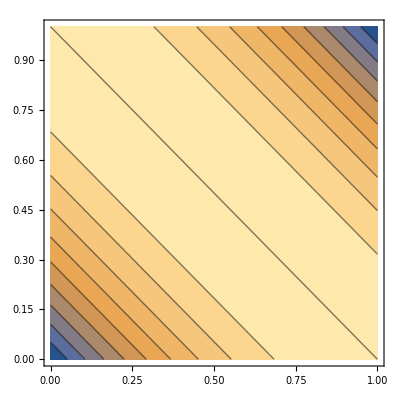

```mathematica
ContourPlot[ℬ[x,y],{x,0,1},{y,0,1}]
```

The probability that an individual becomes high quality dependent on its resources m

```mathematica
𝓆[m_]:=1/2+1/2 Erf[(m-td)/(Sqrt[2]se)]
```

Mortality function

```mathematica
𝓂[m_]:=Min[c+(1-c)m^2,1.0]
```

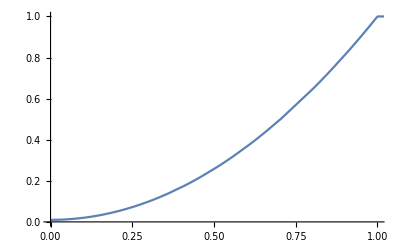

```mathematica
Plot[𝓂[x]/.c->0.01,{x,0,10},PlotRange->{{0,1},{0,1}}]
```

Kin competition function

```mathematica
𝓈[x_]:=Max[1.0-(x/max)^a,0]
```

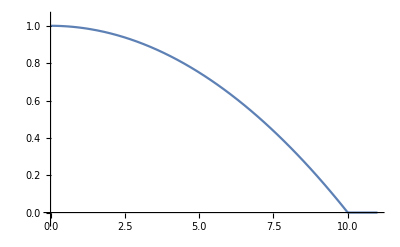

```mathematica
Plot[𝓈[u]/.{a->2,max->10},{u,0,11},PlotRange->{-0.05,1.05}]
```

Juvenile survival:

```mathematica
𝒻[x_]:=1-Exp[-(x-mmin)]
```

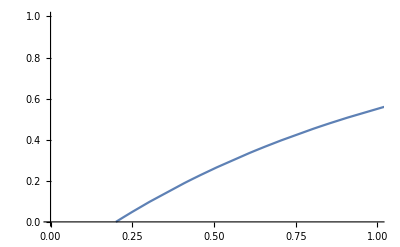

```mathematica
Plot[𝒻[x]/.mmin->0.2,{x,0,10},PlotRange->{{0,1},{0,1}}]
```

## Fitness functions

Expected fitness of a high quality female

```mathematica
Whh=1-μ[ufoc[h]]+1/2(𝓊[1] B[ufoc[h],u[h]]/mbrood[h,h] s[B[ufoc[h],u[h]]/mbrood[h,h]]f[mfoc[h,h]]q[mfoc[h,h]]+𝓊[2] B[ufoc[h],u[l]]/mbrood[h,l] s[B[ufoc[h],u[l]]/mbrood[h,l]]f[mfoc[h,l]]q[mfoc[h,l]])//Simplify;
```

```mathematica
Whl=1/2(𝓊[1] B[ufoc[h],u[h]]/mbrood[h,h] s[B[ufoc[h],u[h]]/mbrood[h,h]]f[mfoc[h,h]](1-q[mfoc[h,h]])+(1-𝓊[1])B[ufoc[h],u[l]]/mbrood[h,l] s[B[ufoc[h],u[l]]/mbrood[h,l]]f[mfoc[h,l]](1-q[mfoc[h,l]]))//Simplify;
```

```mathematica
Wlh=1/2(𝓊[1] B[ufoc[l],u[h]]/mbrood[h,l] s[B[ufoc[l],u[h]]/mbrood[h,l]]f[mfoc[h,l]]q[mfoc[h,l]]+(1-𝓊[1])B[ufoc[l],u[l]]/mbrood[l,l] s[B[ufoc[l],u[l]]/mbrood[l,l]]f[mfoc[l,l]]q[mfoc[l,l]])//Simplify;
```

```mathematica
Wll=1-μ[ufoc[l]]+1/2(𝓊[1] B[ufoc[l],u[h]]/mbrood[h,l] s[B[ufoc[l],u[h]]/mbrood[h,l]]f[mfoc[h,l]](1-q[mfoc[h,l]])+(1-𝓊[1])B[ufoc[l],u[l]]/mbrood[l,l] s[B[ufoc[l],u[l]]/mbrood[l,l]]f[mfoc[l,l]](1-q[mfoc[l,l]]))//Simplify;
```

## Resident transition matrix

Mutant transition matrix

```mathematica
BB={{Whh,Wlh},{Whl,Wll}};
```

Resident transition matrix

```mathematica
A=BB/.{uloc->u,ufoc->u,mbrood->m,mfoc->m};
```

```mathematica
trA=A[[1,1]]+A[[2,2]];
detA=A[[1,1]]*A[[2,2]]-A[[1,2]]A[[2,1]];
```

```mathematica
𝒰eqnev={𝓊[1]λ==A[[1,1]]𝓊[1]+A[[1,2]]𝓊[2],𝓊[2]+𝓊[1]==1,λ==1/2(trA+Sqrt[trA^2-4 detA])};
```

```mathematica
𝒱=Eigenvectors[Transpose[A]];
```

Location of dominant eigenvector

```mathematica
domloc=2
```

2

```mathematica
uvec={{𝓊[1],1-𝓊[1]}};
```

```mathematica
vvecRaw={𝒱[[domloc,All]]}/Total[uvec.Transpose[{𝒱[[domloc,All]]}]];
```

```mathematica
vvecRaw//Dimensions
```

{1,2}

```mathematica
vvec={𝓋[1]->vvecRaw[[1,1]],𝓋[2]->vvecRaw[[1,2]]};
```

## Selection gradient on care in the face of resource transmission q

```mathematica
subslistMut={ufoc->u,uloc->u,mbrood->m,mfoc->m};
```

```mathematica
Δul=1/λ Sum[𝓋[i]𝓊[j](D[BB[[i,j]],ufoc[l]]+D[BB[[i,j]],uloc[l]]R),{i,1,2},{j,1,2}]/.subslistMut/.vvec;
```

```mathematica
Δuh=1/λ Sum[𝓋[i]𝓊[j](D[BB[[i,j]],ufoc[h]]+D[BB[[i,j]],uloc[h]]R),{i,1,2},{j,1,2}]/.subslistMut/.vvec;
```

```mathematica
Δm[q1_,q2_]:=1/λ Sum[𝓋[i]𝓊[j](D[BB[[i,j]],mfoc[q1,q2]]+D[BB[[i,j]],mbrood[q1,q2]]Rbroodoff),{i,1,2},{j,1,2}]/.subslist/.vvec;
```

```mathematica
subsfuncs={μ->𝓂,s->𝓈,q->𝓆,B->ℬ,f->𝒻,R->1/2,Rbroodoff->1/2};
```

## Numerical iterations

```mathematica
iterateSys[cs_,as_,maxs_,{tds_,ses_},mmins_,tend_]:=Module[{substitutedSys,substitutedSys𝒰,uλvec,data,iter,subslist},
substitutedSys={Δul,Δuh,Δm[h,h],Δm[h,l],Δm[l,l]}/.subsfuncs/.{c->cs,a->as,max->maxs,td->tds,se->ses,mmin->mmins};
substitutedSys𝒰=𝒰eqnev/.subsfuncs/.{c->cs,a->as,max->maxs,td->tds,se->ses,mmin->mmins};
data=ConstantArray[0,{tend,8}];
data[[1,All]]={0.3,0.5,2*mmins,2*mmins,2*mmins,1,0.5,0.5};
iter=2;
For[iter=2,iter≤tend,iter++,
subslist={u[l]->data[[iter-1,1]],u[h]->data[[iter-1,2]],m[h,h]->data[[iter-1,3]],m[h,l]->data[[iter-1,4]],m[l,l]->data[[iter-1,5]]};
Print[subslist];
uλvec=FindRoot[substitutedSys𝒰/.subslist,{{λ,1.0},{𝓊[1],0.5},{𝓊[2],0.5}}];
Print[uλvec];
Return[1];
];
Return[data[[1;;iter-1,All]]]
]
```

```mathematica
iterateSys[cs_,as_,maxs_,{tds_,ses_},mmins_,tend_]:=Module[{substitutedSys,substitutedSys𝒰,uλvec,data,iter,subslist},
substitutedSys={Δul,Δuh,Δm[h,h],Δm[h,l],Δm[l,l]}/.subsfuncs/.{c->cs,a->as,max->maxs,td->tds,se->ses,mmin->mmins};
substitutedSys𝒰=𝒰eqnev/.subsfuncs/.{c->cs,a->as,max->maxs,td->tds,se->ses,mmin->mmins};
data=ConstantArray[0,{tend,8}];
data[[1,All]]={0.3,0.5,2*mmins,2*mmins,2*mmins,1,0.5,0.5};
iter=2;
For[iter=2,iter≤tend,iter++,
subslist={u[l]->data[[iter-1,1]],u[h]->data[[iter-1,2]],m[h,h]->data[[iter-1,3]],m[h,l]->data[[iter-1,4]],m[l,l]->data[[iter-1,5]]};
Print[subslist];
uλvec=FindRoot[substitutedSys𝒰/.subslist,{{λ,1.0},{𝓊[1],0.5},{𝓊[2],0.5}}];
Print[{𝓋[1]/.vvec/.uλvec,λ/.uλvec,D[1-μ[ufoc[h]],ufoc[h]]/.subslistMut/.subslist,(1/λ 𝓋[1]𝓊[1]D[B[ufoc[h],u[h]]/mbrood[h,h] s[B[ufoc[h],u[h]]/mbrood[h,h]],ufoc[h]]/.subslistMut/.vvec/.uλvec),B[u[h],u[h]]/m[h,h],B[u[h],u[l]]/m[h,l],B[u[l],u[l]]/m[l,l],s[B[u[h],u[h]]/m[h,h]],s[B[u[h],u[l]]/m[h,l]],s[B[u[l],u[l]]/m[l,l]]}/.subsfuncs/.subslist/.{c->cs,a->as,max->maxs,td->tds,se->ses,mmin->mmins}//N];
Return[10];
data[[iter,All]]=Join[data[[iter-1,1;;5]]+0.01*substitutedSys/.subslist/.uλvec,{λ,𝓊[1],𝓊[2]}/.uλvec];
If[Max[Abs[data[[iter,1;;5]]-data[[iter-1,1;;5]]]]<=1*10^-5,Break[]];
];
Return[data[[1;;iter-1,All]]]
]
```

```mathematica
out=iterateSys[0.01,0.5,100,{.1,3},0.02,3];
```

ReplaceAll::reps: {subslist} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

{u[l]→0.3,u[h]→0.5,m[h,h]→0.04,m[h,l]→0.04,m[l,l]→0.04}

{0.416048,0.978959,-0.99,0.,25.,24.,21.,0.5,0.510102,0.541742}

```mathematica
j
```

```mathematica
out
```

10

```mathematica
jj
```

```mathematica
out
```

FindRoot::nlnum: The function value {Indeterminate,0.,Indeterminate} is not a list of numbers with dimensions {3} at {λ,𝓊[1],𝓊[2]} = {1.,0.5,0.5}.

ReplaceAll::argt: ReplaceAll called with 4 arguments; 1 or 2 arguments are expected.

FindRoot::nlnum: The function value {Indeterminate,0.,Indeterminate} is not a list of numbers with dimensions {3} at {λ,𝓊[1],𝓊[2]} = {1.,0.5,0.5}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

ReplaceAll::argt: ReplaceAll called with 4 arguments; 1 or 2 arguments are expected.

General::stop: Further output of ReplaceAll::argt will be suppressed during this calculation.

{{0.5,0.2,0.002,0.002,0.002,1,0.5,0.5},{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,0.9996,1.00914×10^-13,1.},{ReplaceAll[{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate},FindRoot[substitutedSys𝒰$12411/.subslist$12411,{{λ,1.},{𝓊[1],0.5},{𝓊[2],0.5}}],{λ,𝓊[1],𝓊[2]},FindRoot[substitutedSys𝒰$12411/.subslist$12411,{{λ,1.},{𝓊[1],0.5},{𝓊[2],0.5}}]],ReplaceAll[{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate},FindRoot[substitutedSys𝒰$12411/.subslist$12411,{{λ,1.},{𝓊[1],0.5},{𝓊[2],0.5}}],{λ,𝓊[1],𝓊[2]},FindRoot[substitutedSys𝒰$12411/.subslist$12411,{{λ,1.},{𝓊[1],0.5},{𝓊[2],0.5}}]],ReplaceAll[{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate},FindRoot[substitutedSys𝒰$12411/.subslist$12411,{{λ,1.},{𝓊[1],0.5},{𝓊[2],0.5}}],{λ,𝓊[1],𝓊[2]},FindRoot[substitutedSys𝒰$12411/.subslist$12411,{{λ,1.},{𝓊[1],0.5},{𝓊[2],0.5}}]],ReplaceAll[{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate},FindRoot[substitutedSys𝒰$12411/.subslist$12411,{{λ,1.},{𝓊[1],0.5},{𝓊[2],0.5}}],{λ,𝓊[1],𝓊[2]},FindRoot[substitutedSys𝒰$12411/.subslist$12411,{{λ,1.},{𝓊[1],0.5},{𝓊[2],0.5}}]],ReplaceAll[{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate},FindRoot[substitutedSys𝒰$12411/.subslist$12411,{{λ,1.},{𝓊[1],0.5},{𝓊[2],0.5}}],{λ,𝓊[1],𝓊[2]},FindRoot[substitutedSys𝒰$12411/.subslist$12411,{{λ,1.},{𝓊[1],0.5},{𝓊[2],0.5}}]],ReplaceAll[{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate},FindRoot[substitutedSys𝒰$12411/.subslist$12411,{{λ,1.},{𝓊[1],0.5},{𝓊[2],0.5}}],{λ,𝓊[1],𝓊[2]},FindRoot[substitutedSys𝒰$12411/.subslist$12411,{{λ,1.},{𝓊[1],0.5},{𝓊[2],0.5}}]],ReplaceAll[{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate},FindRoot[substitutedSys𝒰$12411/.subslist$12411,{{λ,1.},{𝓊[1],0.5},{𝓊[2],0.5}}],{λ,𝓊[1],𝓊[2]},FindRoot[substitutedSys𝒰$12411/.subslist$12411,{{λ,1.},{𝓊[1],0.5},{𝓊[2],0.5}}]],ReplaceAll[{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate},FindRoot[substitutedSys𝒰$12411/.subslist$12411,{{λ,1.},{𝓊[1],0.5},{𝓊[2],0.5}}],{λ,𝓊[1],𝓊[2]},FindRoot[substitutedSys𝒰$12411/.subslist$12411,{{λ,1.},{𝓊[1],0.5},{𝓊[2],0.5}}]]}}

```mathematica
Max[Abs[out[[1,All]]-out[[2,All]]][[1;;5]]]≤1*10^-5
```

FindRoot::nlnum: The function value {Indeterminate,0.,Indeterminate} is not a list of numbers with dimensions {3} at {λ,𝓊[1],𝓊[2]} = {1.,0.5,0.5}.

ReplaceAll::argt: ReplaceAll called with 4 arguments; 1 or 2 arguments are expected.

FindRoot::nlnum: The function value {Indeterminate,0.,Indeterminate} is not a list of numbers with dimensions {3} at {λ,𝓊[1],𝓊[2]} = {1.,0.5,0.5}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

ReplaceAll::argt: ReplaceAll called with 4 arguments; 1 or 2 arguments are expected.

General::stop: Further output of ReplaceAll::argt will be suppressed during this calculation.

Indeterminate≤1/100000